```mathematica
SetDirectory["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\Errors"]
```

\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors

```mathematica
getCharge[filename_]:=StringCases[filename,"*_"~~q:(DigitCharacter|"."|"-")..~~"*":>ToExpression[q]][[1]]
```

```mathematica
readHDF5Beam[filename_,opts___Rule]:=Block[{unrotate,verbose,cols,startposition,rotation},
unrotate=Global`HDF5Normalise/.{opts}/.{Global`HDF5Normalise->False};
verbose=Global`HDF5Verbose/.{opts}/.{Global`HDF5Verbose->False};
cols=Import[filename,"/beam/columns"];
Clear[Evaluate[#]]&/@cols;
beamdata=Transpose[Import[filename,"/beam/beam"]];
startposition=Import[filename,"/Parameters/Starting_Position"];
rotation=Import[filename,"/Parameters/Rotation"];
If[unrotate,
beamdata[[{1,2,3}]]=Transpose[(#-startposition&/@Transpose[beamdata[[{1,2,3}]]]).RotationMatrix[rotation,{0,1,0}]];
beamdata[[{4,5,6}]]=Transpose[((#&/@Transpose[beamdata[[{4,5,6}]]]).RotationMatrix[rotation,{0,1,0}])];
];
MapThread[(Evaluate[Symbol@#1]=#2)&,{cols,beamdata}];
params=Import[filename,"/Parameters"];
Clear[Evaluate[StringReplace[#1,{"_"->"£","-"->"$"}]]]&/@Keys[params];
MapThread[(Evaluate[Symbol@StringReplace[#1,{"_"->"£","-"->"$"}]]=#2)&,{Keys[params],Values[params]}];
If[verbose,
Print["Parameter(s) Assigned: ",Keys[params]];
Print["Variables(s) Assigned: ",cols];
];
]
```

```mathematica
cp:=√(cpx^2+cpy^2+cpz^2)
```

## Generate Gaussian Beam

```mathematica
<<generateGaussianBeamDistribution`
```

```mathematica
2^(3*6)
```

262144

```mathematica
beam=generateGaussianBeamDistribution[2^(3*6),{1,1,0,10^-3},{0,1,0,1},{0,0,0,0},{0,0,0,0}];
```

```mathematica
ListPlot[beam[[All,{1,2}]]]
```

-Graphics-

```mathematica
UnitConvert[Quantity[0.08,"mm"]/Quantity["SpeedOfLight"],"ps"]
```

0.266851 ps

```mathematica
0.1/250
```

0.0004

```mathematica
<<sddsInterpret`
```

```mathematica
sddsInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA\\Elegant_Genesis\\gaussianBeam\\CLA-FMS-APER-01.sdds",sddsVerbose->True]
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {x, xp, y, yp, t, p, particleID}

Parameters (Re)Assigned: {Step, pCentral, Charge, Particles, IDSlotsPerBunch}

```mathematica
0.511Mean[p]
```

240.

## Charge

```mathematica
getCharge[filename_]:=StringCases[filename,"*_"~~q:(DigitCharacter|"."|"-")..~~"*":>ToExpression[q]][[1]]
```

```mathematica
files=FileNames["CLA-FMS-APER-01.hdf5",{"\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\Errors\\charge*"},2]
```

{\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_0.91\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_0.92\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_0.93\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_0.94\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_0.95\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_0.96\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_0.97\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_0.98\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_0.99\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_0.9\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_1.01\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_1.02\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_1.03\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_1.04\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_1.05\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_1.06\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_1.07\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_1.08\CLA-FMS-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\charge_1.0\CLA-FMS-APER-01.hdf5}

```mathematica
readHDF5Beam[files[[1]],HDF5Verbose->True]
Mean[t]
```

Parameter(s) Assigned: {Rotation,Source,Starting_Position,centered,code,npart,particle_mass,total_charge}

Variables(s) Assigned: {x,y,z,cpx,cpy,cpz,t,q}

-1.65041×10^-7

```mathematica
charget=Block[{},
readHDF5Beam[#,HDF5Verbose->False];
{getCharge[#],-10^12 total£charge,Mean[z],StandardDeviation[t]}
]&/@files
```

{{0.91,229.32,49.4778,2.55864×10^-13},{0.92,229.32,49.4778,2.55238×10^-13},{0.93,233.415,49.4778,2.57419×10^-13},{0.94,233.415,49.4778,2.57419×10^-13},{0.95,237.51,49.4778,2.59632×10^-13},{0.96,241.605,49.4778,2.61833×10^-13},{0.97,241.605,49.4778,2.61833×10^-13},{0.98,245.7,49.4778,2.64022×10^-13},{0.99,245.7,49.4778,2.64022×10^-13},{0.9,225.225,49.4778,2.5299×10^-13},{1.01,253.89,49.4778,2.68583×10^-13},{1.02,253.89,49.4778,2.68583×10^-13},{1.03,257.985,49.4778,2.70802×10^-13},{1.04,257.985,49.4778,2.70802×10^-13},{1.05,262.08,49.4778,2.72901×10^-13},{1.06,266.175,49.4778,2.75015×10^-13},{1.07,266.175,49.4778,2.75015×10^-13},{1.08,270.27,49.4778,2.77157×10^-13},{1.,249.795,49.4778,2.6641×10^-13}}

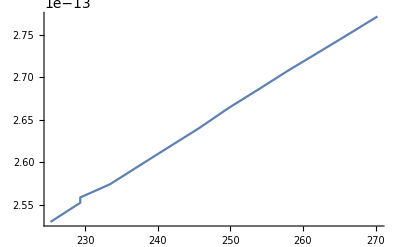

```mathematica
ListLinePlot[Sort[charget[[All,{2,4}]]]]
```

## Initial_t

```mathematica
gett[filename_]:=StringCases[filename,"_"~~t:(DigitCharacter|"."|"-")..~~"ps":>ToExpression[t]][[1]]
```

```mathematica
files=FileNames["CLA-S02-APER-01.hdf5",{"\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\Errors\\initial_t*"},2]
```

{\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_t_-0.8ps\CLA-S02-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_t_-0.9ps\CLA-S02-APER-01.hdf5,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_t_-1ps\CLA-S02-APER-01.hdf5}

```mathematica
gett[files[[1]]]
```

-0.8

```mathematica
readHDF5Beam[files[[1]],HDF5Verbose->True]
t0=Mean[t]
```

Parameter(s) Assigned: {Rotation,Source,Starting_Position,centered,code,npart,particle_mass,total_charge}

Variables(s) Assigned: {x,y,z,cpx,cpy,cpz,t,q}

1.12472×10^-8

```mathematica
E0=QuantityMagnitude[UnitConvert[Quantity["ElectronMass"] Quantity["SpeedOfLight"]^2],"eV"]
```

510998.9

```mathematica
En:=√(cp^2+E0^2)
```

```mathematica
Mean[En]
```

3.51294×10^7

```mathematica
initialt=Block[{},
readHDF5Beam[#,HDF5Verbose->False,HDF5Normalise->False];
{gett[#],-10^12 total£charge,Mean[t]-t0,10^12 StandardDeviation[t],10^-6 Mean[cp],10^-6 StandardDeviation[cp]}
]&/@files
```

{{-0.8,249.795,0.,1.64387,35.1257,0.166862},{-0.9,249.795,8.53763×10^-16,1.64305,35.1132,0.16802},{-1,249.795,1.88531×10^-15,1.63373,35.098,0.167135}}

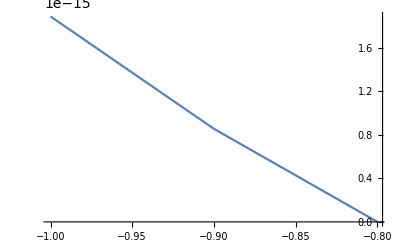

```mathematica
ListLinePlot[{Sort[initialt[[All,{1,3}]]]}]
```

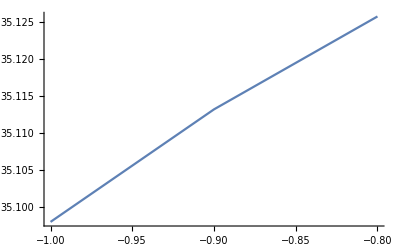

```mathematica
ListLinePlot[{Sort[initialt[[All,{1,5}]]]}]
```

## Initial_t_testing

```mathematica
<<astrainterpret`
```

```mathematica
SetDirectory["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\Errors\\initial_t_-1ps"]
```

\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_t_-1ps

```mathematica
emitfiles=Sort[FileNames["*.Zemit.001"],FileDate[#1]<FileDate[#2]&]
```

{injector400.Zemit.001,S02.Zemit.001,L02.Zemit.001,S03.Zemit.001,L03.Zemit.001,S04.Zemit.001,L4H.Zemit.001,S05.Zemit.001,S06.Zemit.001,L04.Zemit.001,S07.Zemit.001}

```mathematica
ASTRAemitInterpret[emitfiles,ASTRAVerbose->True]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

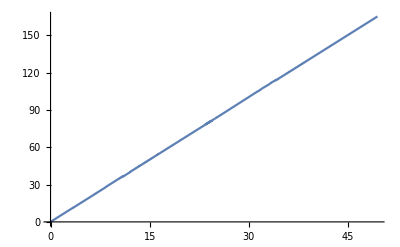

```mathematica
ListLinePlot[{Transpose[{z,t}]}]
```

```mathematica
emitfiles=Sort[FileNames["S07.Zemit.001",{"\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\Errors\\initial_t_*"},1],FileDate[#1]<FileDate[#2]&]
```

{\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_t_-0.8ps\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_t_-1ps\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_t_-0.9ps\S07.Zemit.001}

```mathematica
ASTRAemitInterpret[emitfiles[[2]],ASTRAVerbose->True]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
Last[t]
```

165.06

## Initial_x_testing

```mathematica
<<astrainterpret`
```

```mathematica
getx[filename_]:=StringCases[filename,"_"~~x:(DigitCharacter|"."|"-"|"e")..~~"mm":>ImportString[x,"Table"][[1,1]]][[1]]
```

```mathematica
SetDirectory["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\Errors\\initial_x_-1mm"]
```

\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_-1mm

```mathematica
emitfiles=Sort[FileNames["*.Zemit.001"],FileDate[#1]<FileDate[#2]&]
```

{injector400.Zemit.001,S02.Zemit.001,L02.Zemit.001,S03.Zemit.001,L03.Zemit.001,S04.Zemit.001,L4H.Zemit.001,S05.Zemit.001,S06.Zemit.001,L04.Zemit.001,S07.Zemit.001}

```mathematica
ASTRAemitInterpret[emitfiles,ASTRAVerbose->True]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

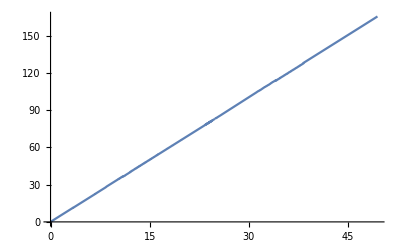

```mathematica
ListLinePlot[{Transpose[{z,t}]}]
```

```mathematica
emitfiles=Sort[FileNames["S07.Zemit.001",{"\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\Errors\\initial_x_*"},1],FileDate[#1]<FileDate[#2]&]
```

{\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_-1mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_-0.9mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_-0.8mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_-0.7mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_-0.6mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_-0.5mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_-0.4mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_-0.3mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_-0.2mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_-0.1mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_-1.38777878078e-16mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_0.1mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_0.2mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_0.3mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_0.4mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_0.5mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_0.6mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_0.7mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_0.8mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_0.9mm\S07.Zemit.001,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\Errors\initial_x_1.0mm\S07.Zemit.001}

```mathematica
getx[emitfiles[[11]]]
```

{-1.38778×10^-16}

```mathematica
ASTRAemitInterpret[emitfiles[[11]],ASTRAVerbose->False];
t0=Last[t];z0=Last[z]
```

49.478

```mathematica
xinitialdata=Block[{},
ASTRAemitInterpret[#,ASTRAVerbose->False];
{getx[#],Last[t]-t0,Last[z]-z0}
]&/@emitfiles
```

{{-1,0.4,0.},{-0.9,0.21,0.},{-0.8,0.12,0.},{-0.7,0.07,0.},{-0.6,0.04,0.},{-0.5,0.02,0.},{-0.4,0.01,0.},{-0.3,0.,0.},{-0.2,0.,0.},{-0.1,0.,0.},{-1.38778×10^-16,0.,0.},{0.1,0.,0.},{0.2,0.,0.},{0.3,0.01,0.},{0.4,0.01,0.},{0.5,0.02,0.},{0.6,0.04,0.},{0.7,0.08,0.},{0.8,0.13,0.},{0.9,0.24,0.},{1.,0.46,0.}}

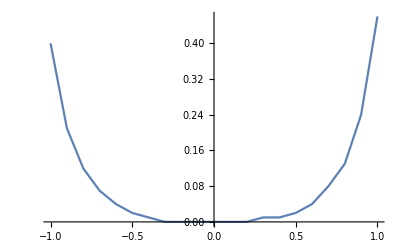

```mathematica
ListLinePlot[xinitialdata[[All,{1,2}]]]
```